## First the definition

```mathematica
JoinGraphs[f_,g_,h_]:=Block [{edges,full,
edgef=EdgeList[f],
edgeg=EdgeList[g],
edgeh=EdgeList[h],
greenEdges,
blueEdges,
greenStarts,
blueToGreen=Association[] (* gives for each blue (contract) vertex a vertex in the "with" graph *),
orangeEgdes
},
(* greenedges are the ones connecting the with with the contract So each green starts in the "with" and ends
   in the "contract" *)
greenEdges=SetDifference[SetDifference[edgeg,edgef],edgeh];
greenStarts=Map[(blueToGreen[#[[2]]]=#[[1]];#[[1]])&,greenEdges];
blueEdges=edgeh;
edges=Join[
Table[e->Directive[{Red}],{e,edgef}],
Table[e->Directive[{Darker[Green]}],{e,greenEdges}],
Table[e->Directive[{Thick,Blue}],{e,blueEdges}]
];
orangeEgdes=Map[blueToGreen[#[[1]]]->blueToGreen[#[[2]]]&,blueEdges];
(* rewrite the orange edges *)
edges=Table[If[MemberQ[orangeEgdes,edge[[1]]],edge[[1]]->Directive[{Thick,Purple}],edge],{edge,edges}];

(* now combine the graphs and emit*)
full=GraphUnion[f,g,h];
(*full=Graph[VertexList[full],MapAll[SortEdge,EdgeList[full]]];*)
Graph[VertexList[full],EdgeList[full],VertexLabels->Table[v->If[SymbolLevel[v]==4,Rotate[Framed[SymbolToLabel2[v],FrameStyle->If[VertexQ[h,v],Directive[Blue,Dashed],Directive[Red,Thickness[0.001]]]],Pi/6],Rotate[SymbolToLabel2[v],Pi/6]],{v,VertexList[full]}],EdgeStyle->edges,
VertexStyle->Join[
Table[v->Red,{v,VertexList[f]}],
Table[v->Blue,{v,VertexList[h]}]]
]
]
```

```mathematica
SymbolToColumn[s_]:=Grid[Map[Map[Style[#,10,FontFamily->"Consolas"]&,#]&,SymbolToSets[s]], Spacings->{.4,0}, Alignment->Center, Frame->All, FrameStyle->Directive[Orange,12], Background->White]
```

```mathematica
SymbolToColumn[v1x2x3x45]
```

1 | 
2 | 
3 | 
4 | 5

```mathematica
DrawWithWithoutAndContract[g_,imagesize_:350]:=Block[{edges,full,implied={},mpg, coordinates={}, currentGraph,all,localcoordinates,form,ffull},
edges=EdgeList[g];
mpg=CollectMPGEdges[g];
form=DeleteDuplicates[Flatten[Table[Map[SymbolReplace[#,e]&,FindFullFormula[GContract[g,e]]],{e,Map[UndirectedEdge[#[[1]],#[[2]]]&,Subsets[VertexList[g],{2}]]}]]];
form=Table[Map[SymbolReplace[#,e]&,FindFullFormula[GContract[g,e]]],{e,EdgeList[g]}];
form=Join[form,FindFullFormula[g]];
AppendTo[form,SetsToSymbol[Table[{i},{i,VertexCount[g]}]]];
form=Sort[DeleteDuplicates[Flatten[form]],CompareSymbols];
all=FormulaGraphReverse2[form];
coordinates=Mix[VertexList[all],GraphEmbedding[all]];

ffull=FindFullFormula[g];
Monitor[
Table[With[{
without=Graph[EdgeDelete[g,e]],
contract =Graph[EdgeContract[g,e]],
with=Graph[g]
},
With[
{
fwithout=FindFullFormula[without],
fcontract=Map[SymbolReplace[#,e]&,FindFullFormula[contract]]
},
implied=Join[implied,ImpliedNodes[fcontract,ffull]];
currentGraph=JoinGraphs[
FormulaGraphReverse2[ffull],
FormulaGraphReverse2[fwithout],
FormulaGraphReverse2[fcontract]
];
localcoordinates=(VertexList[currentGraph]/.coordinates);
currentGraph=Graph[
currentGraph,  ImageSize->imagesize,VertexCoordinates->localcoordinates, AspectRatio->1/GoldenRatio
];
Labeled[currentGraph,If[MemberQ[mpg,e],Style[e,Red],e]]
]
],{e,Sort[Map[SortEdge,edges]]}],
e]
]
```

```mathematica
Mix[head_,value_]:=Table[head[[i]]->value[[i]],{i,Length[head]}]
```

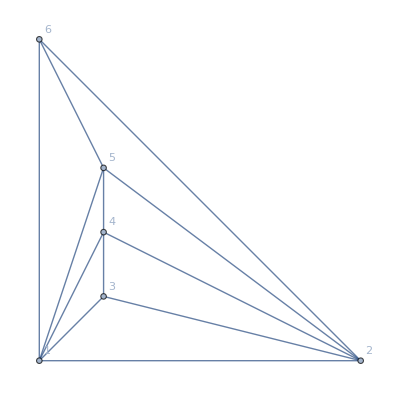
```mathematica
Mix[VertexList[-Graphics-],GraphEmbedding[-Graphics-]]
```

{1→{0.,0.},2→{5.,0.},3→{1.,1.},4→{1.,2.},5→{1.,3.},6→{0.,5.}}

## Now the calc

```mathematica
MinimalGraph[5]
```

-Graphics-

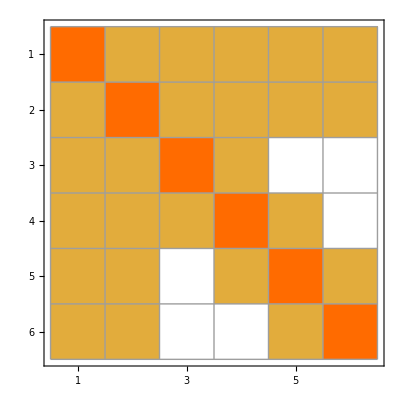

```mathematica
MatrixPlot[AdjacencyMatrix[MinimalGraph[5]]+2*IdentityMatrix[6], Mesh->All]
```

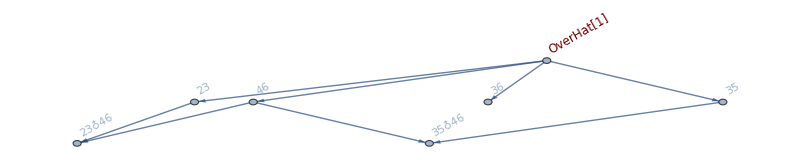
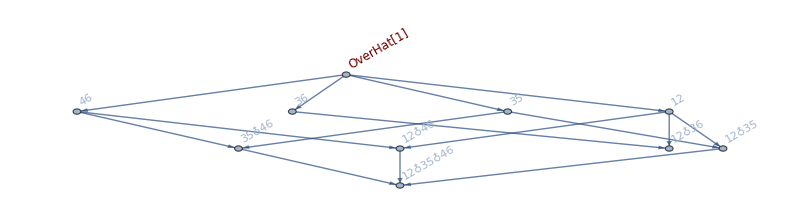
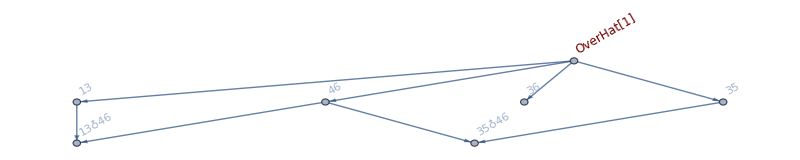
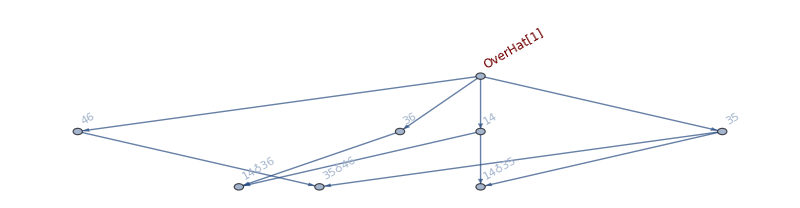
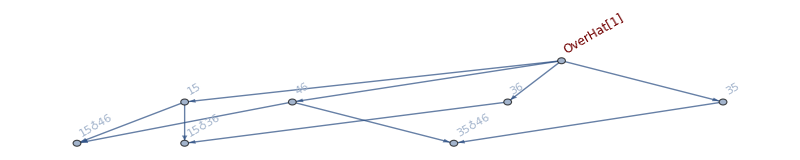
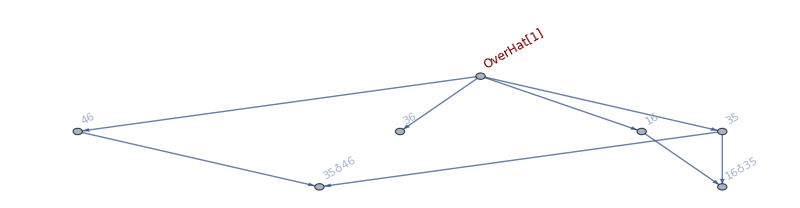
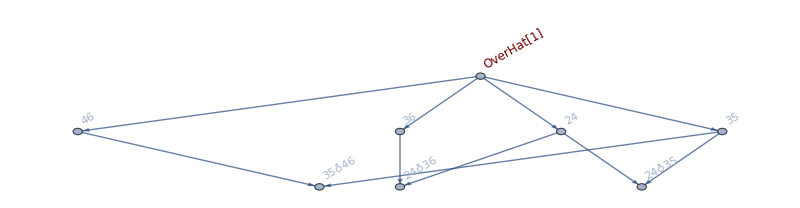
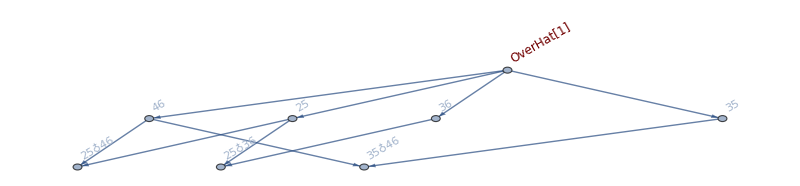
{-Graphics-2<->3,-Graphics-1<->2,-Graphics-1<->3,-Graphics-1<->4,-Graphics-1<->5,-Graphics-1<->6,-Graphics-2<->4,-Graphics-2<->5,-Graphics-2<->6,-Graphics-3<->4,-Graphics-4<->5,-Graphics-5<->6}

```mathematica
DrawWithWithoutAndContract[MinimalGraph[5],800]
```

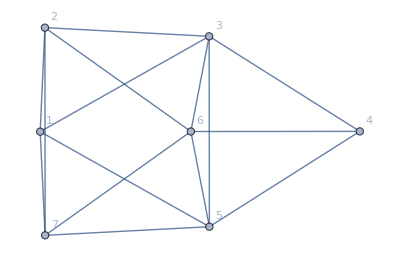

```mathematica
Graph[ReadGrof[6],VertexLabels->"Name"]
```

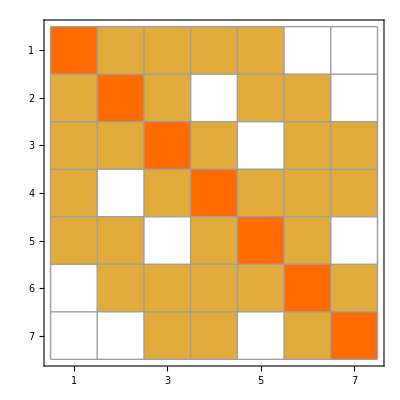

```mathematica
MatrixPlot[AdjacencyMatrix[ReadGrof[6]]+2*IdentityMatrix[7], Mesh->All]
```

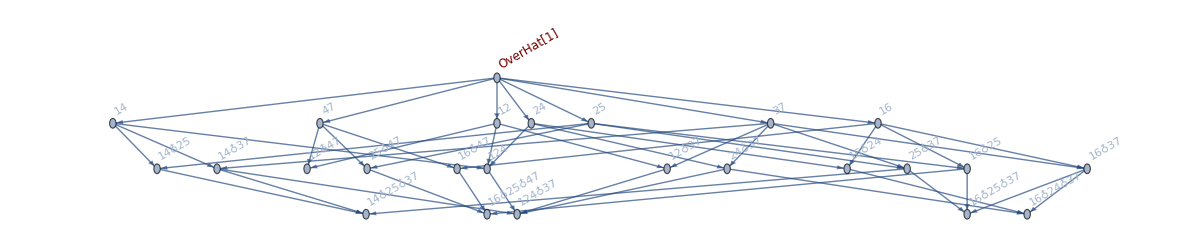
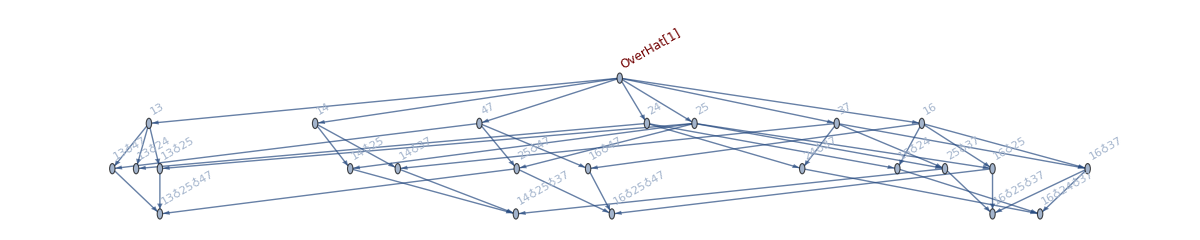
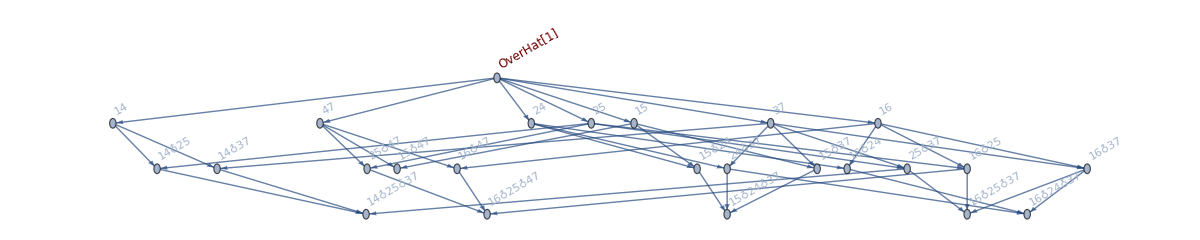
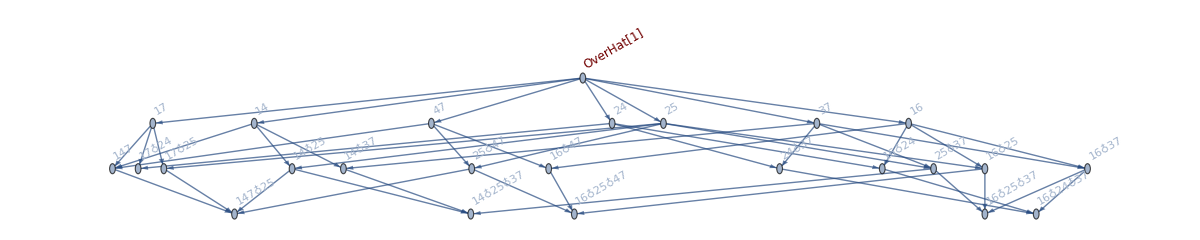
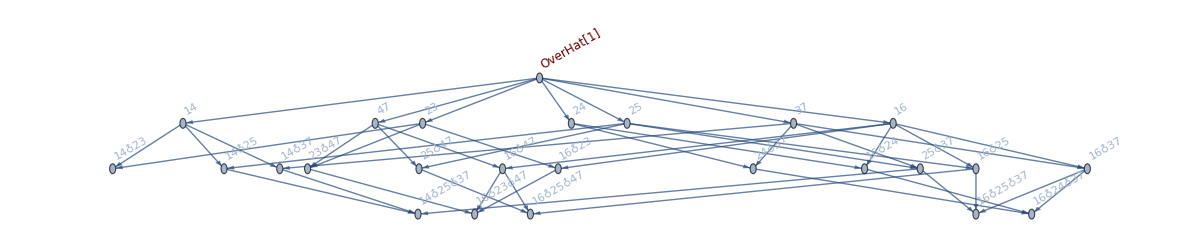
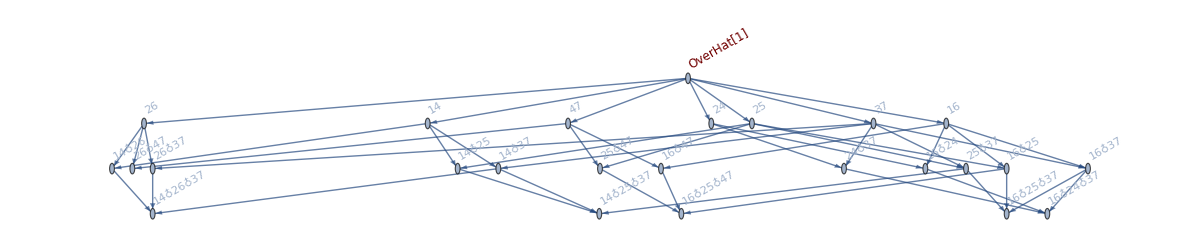
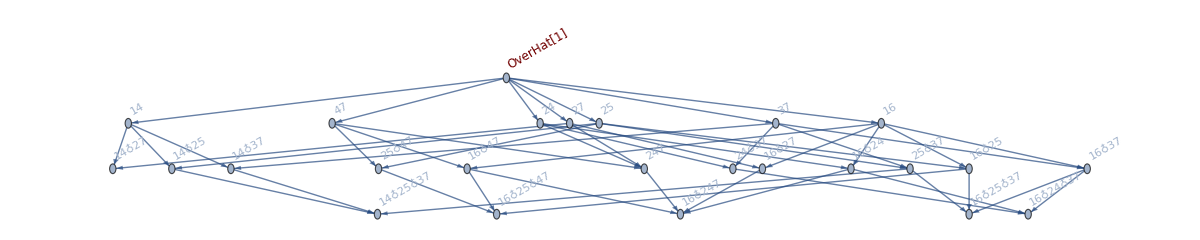
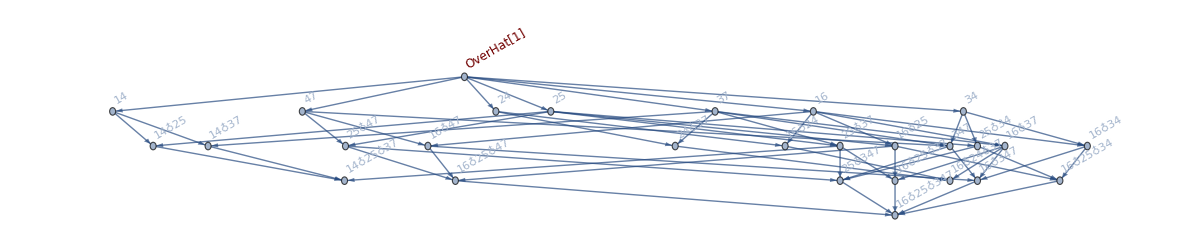
{-Graphics-1<->2,-Graphics-1<->3,-Graphics-1<->5,-Graphics-1<->7,-Graphics-2<->3,-Graphics-2<->6,-Graphics-2<->7,-Graphics-3<->4,-Graphics-3<->5,-Graphics-3<->6,-Graphics-4<->5,-Graphics-4<->6,-Graphics-5<->6,-Graphics-5<->7,-Graphics-6<->7}

```mathematica
DrawWithWithoutAndContract[ReadGrof[6],1200]
```